# Bosonic Algebra, Stabilizers, and Interferometers: Keynote Examples

Bosonic algebra. Wolfram QuantumFramework now computes exactly in the Weyl algebra of light and oscillators: it disentangles squeezers, beam splitters and even cubic exponentials into normal-ordered closed forms, identities that physicists otherwise derive by hand from commutators, valid at every photon number and never truncated to a finite matrix.

Stabilizer formalism. Wolfram QuantumFramework runs Clifford circuits on the stabilizer tableau, n Pauli generators instead of 2^n amplitudes, so a thousand-qubit state takes milliseconds and its entanglement comes out as an exact integer from linear algebra over 𝔽_2. When a non-Clifford T gate arrives, the same object switches to an exact superposition of stabilizer states instead of failing.

QuantumInterferometer. In Wolfram QuantumFramework a beam splitter is an SU(2) rotation of the photon modes, so its photon-counting amplitudes are Wigner D-functions returned symbolically with the photon numbers themselves left as variables. One exact formula covers Hong-Ou-Mandel interference for every n, where other photonics software computes one photon count at a time, numerically.

Install the QuantumFramework:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF", ForceVersionInstall -> True]
Needs["Wolfram`QuantumFramework`"]
Needs["Wolfram`QuantumFramework`SecondQuantization`"]
```

PacletObject[…]

## Bosonic algebra

Operators of light and oscillators, ordered and disentangled exactly. The field variables are the formal symbols a and b; their creation operators are a^† and b^†. Every result is an operator identity, valid at every photon number, with no Fock-space cutoff.

### 1. Squeezing, factored

The squeeze operator Ŝ(ξ)=exp [1/2(ξ^*(â)^2-ξ (â)^(†2))], ξ=r e^iθ. One call returns its exact factorization into creation, number and annihilation parts, the identity squeezed-light calculations rest on, for every r and θ:

Ŝ(ξ)=(e^(-1/2 e^iθ tanh (r) (â)^(†2))) ((sech (r))^((â)^†â+1/2)) (e^(1/2 e^-iθ tanh (r) (â)^2))

```mathematica
BosonicExpOrder[Exp[1/2 r E^(-I θ) a**a - 1/2 r E^(I θ) SuperDagger[a]**SuperDagger[a]], Assumptions -> r > 0]
```

ⅇ^(-1/2 ⅇ^(ⅈ θ) NonCommutativeMultiply(a^†)2** Tanh[r])**Sech[r]^(1/2+a^†**a)**ⅇ^(1/2 ⅇ^(-ⅈ θ) NonCommutativeMultiplya2** Tanh[r])

### 2. Two-mode squeezing

The two-mode squeezer (Ŝ)_2(ξ)=exp (ξ^*â b̂-ξ (â)^†(b̂)^†), the source of entangled photon pairs, disentangled just as exactly:

(Ŝ)_2(ξ)=sech (r) (e^(-e^iθ tanh (r) (â)^†(b̂)^†)) ((sech (r))^((â)^†â+(b̂)^†b̂)) (e^(e^-iθ tanh (r) â b̂))

```mathematica
BosonicExpOrder[Exp[r E^(-I θ) a**b - r E^(I θ) SuperDagger[a]**SuperDagger[b]], Assumptions -> r > 0]
```

ⅇ^(-ⅇ^(ⅈ θ) a^†**b^† Tanh[r])**Sech[r]^(a^†**a+b^†**b)**ⅇ^(ⅇ^(-ⅈ θ) a**b Tanh[r]) Sech[r]

### 3. A beam splitter between two modes

Mode mixing exp (α â(b̂)^†+β (â)^†b̂) with arbitrary complex α,β and Ω=√αβ: one exact operator identity covers every photon number:

e^(α â(b̂)^†+β(â)^†b̂)=(e^((βtanh Ω)/Ω(â)^†b̂)) ((cosh Ω)^((b̂)^†b̂-(â)^†â)) (e^((αtanh Ω)/Ω â(b̂)^†))

```mathematica
Simplify[BosonicExpOrder[Exp[α a**SuperDagger[b] + β SuperDagger[a]**b]]]
```

ⅇ^((β a^†**b Tanh[√(α β)])/(√(α β)))**Cosh[√(α β)]^(-a^†**a+b^†**b)**ⅇ^((α a**b^† Tanh[√(α β)])/(√(α β)))

### 4. A nonlinear exponential

An exponential cubic in the ladder operators, e^(k (â)^†â(â)^†), outside the quadratic cases that standard disentangling identities cover, still has an exact normal-ordered form:

e^(k (â)^†â(â)^†)= :(1/(1-k(â)^†)) (exp [(1/(1-k(â)^†)-1)(â)^†â]):

```mathematica
BosonicExpOrder[Exp[k SuperDagger[a]**a**SuperDagger[a]]]
```

NormalOrdered[1/(1-k a^†)**ⅇ^((-1+1/(1-k a^†))**a^†**a)]

Its normal-ordered series in k, term by term:

```mathematica
Collect[BosonicExpOrder[Exp[k SuperDagger[a]**a**SuperDagger[a]]]["Series", k, 3], k]
```

1+k^2 (NonCommutativeMultiply(a^†)2**+2 NonCommutativeMultiply(a^†)3****a+1/2 NonCommutativeMultiply(a^†)4****NonCommutativeMultiplya2**)+k^3 (NonCommutativeMultiply(a^†)3**+3 NonCommutativeMultiply(a^†)4****a+3/2 NonCommutativeMultiply(a^†)5****NonCommutativeMultiplya2**+1/6 NonCommutativeMultiply(a^†)6****NonCommutativeMultiplya3**)+k (NonCommutativeMultiply(a^†)2****a+a^†)

### 5. Reordering a product

Reordering e^(k(â)^2)e^(m(â)^(†2)) into normal order, a page of commutator algebra by hand, in one call:

(e^(k(â)^2)) (e^(m(â)^(†2)))=1/(√(1-4km)) (e^(m/(1-4km)(â)^(†2))) ((1-4km)^(-(â)^†â)) (e^(k/(1-4km)(â)^2))

```mathematica
BosonicExpOrder[Exp[k a**a]**Exp[m SuperDagger[a]**SuperDagger[a]]]
```

(ⅇ^((m NonCommutativeMultiply(a^†)2**)/(1-4 k m))**(1-4 k m)^(-a^†**a)**ⅇ^((k NonCommutativeMultiplya2**)/(1-4 k m)))/(√(1-4 k m))

and a displacement into anti-normal order, e^(λ â+β(â)^†)=e^(-βλ/2) (e^(λ â)) (e^(β(â)^†)), the ordering behind the Husimi Q function:

```mathematica
BosonicExpOrder[Exp[λ a + β SuperDagger[a]], "Ordering" -> "Antinormal"]
```

ⅇ^(-(β λ)/2) ⅇ^(a λ)**ⅇ^(β a^†)

## Stabilizer formalism

A Clifford state stored as the group of Pauli operators that fix it, P̂ ψ=ψ: n generators instead of 2^n amplitudes, so the cost grows polynomially in the number of qubits, not exponentially.

### 6. Same circuit, different engine

A five-qubit cluster-state circuit: Hadamards, then controlled-Z gates down the chain:

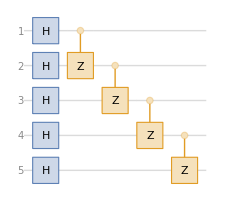

```mathematica
cluster5 = QuantumCircuitOperator[Join[Thread["H" -> Range[5]], {"CZ" -> {1, 2}, "CZ" -> {2, 3}, "CZ" -> {3, 4}, "CZ" -> {4, 5}}]];
cluster5["Diagram"]
```

The same circuit on the stabilizer engine, one option away, returns a tableau of generators instead of 2^5 amplitudes:

```mathematica
stab5 = cluster5[Method -> "Stabilizer"]
```

PauliStabilizer[…]

Its generators are (K̂)_v=(X̂)_v∏_(w∼v) (Ẑ)_w, one per site:

```mathematica
stab5["PauliForm"]
```

{XZIII,ZXZII,IZXZI,IIZXZ,IIIZX}

Expectation values come straight from the generators, exactly and with no state vector: ⟨(K̂)_1⟩=1, while (X̂)_1(X̂)_2, which anticommutes with (K̂)_1, averages to zero:

```mathematica
<|"XZIII" -> stab5["Expectation", "XZIII"], "XXIII" -> stab5["Expectation", "XXIII"]|>
```

<|XZIII→1,XXIII→0|>

### 7. A thousand qubits, exact entanglement

Twenty thousand random Clifford gates on 1000 qubits, a state with 2^1000 amplitudes, then its entanglement entropy as an exact integer, read off the generators restricted to half the chain A:

S(A)=rank_𝔽_2 (G_A)-A

A seeded random stream of Hadamard, CNOT and phase gates:

```mathematica
nq = 1000;
SeedRandom[1];
gates = Flatten@Table[{"H" -> RandomInteger[{1, nq}], "CNOT" -> RandomSample[Range[nq], 2], "S" -> RandomInteger[{1, nq}]}, {6666}];
Length@gates
```

19998

Applied to the tableau in one compiled pass, timed:

```mathematica
(big = PauliStabilizer[nq]["ApplyCircuit", gates]) // AbsoluteTiming
```

{0.021566,PauliStabilizer[…]}

The half-chain entropy, an exact integer rather than a sampled estimate:

```mathematica
big["Entropy", Range[nq/2]]
```

496

### 8. An 800-qubit GHZ state

The state GHZ=(0^(⊗800)+1^(⊗800))/√2, built straight from its circuit name; a dense simulator would need 2^800 amplitudes:

```mathematica
g = PauliStabilizer["GHZ"[800]]
```

PauliStabilizer[…]

It is fixed by (X̂)^(⊗800):

```mathematica
g["Expectation", StringJoin@ConstantArray["X", 800]]
```

1

and by (Ẑ)_1(Ẑ)_800, which links the two ends of the chain:

```mathematica
g["Expectation", "Z" <> StringJoin@ConstantArray["I", 798] <> "Z"]
```

1

### 9. Circuit, tableau, state, circuit

A three-qubit cluster circuit:

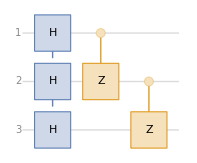

```mathematica
cluster3 = QuantumCircuitOperator[{"H" -> Range[3], "CZ", "CZ" -> {2, 3}}];
cluster3["Diagram"]
```

The stabilizer engine turns it into a tableau:

```mathematica
stab3 = cluster3[Method -> "Stabilizer"]
```

PauliStabilizer[…]

Expanded, the tableau gives exactly, not approximately, the state the default engine computes, ψ=1/(2 √2)∑_(x∈{0,1}^3) (-1)^(x_1 x_2+x_2 x_3)x_1 x_2 x_3:

```mathematica
QuantumState[stab3]["StateVector"] === cluster3[]["StateVector"]
```

True

And the tableau synthesizes a circuit that prepares it, closing the loop from circuit to tableau to state to circuit:

```mathematica
stab3["Circuit"]["Diagram"]
```

-Graphics-

### 10. Beyond Clifford

A T gate leaves the stabilizer group. Instead of failing or approximating, the engine switches to a superposition of stabilizer states:

```mathematica
fr = QuantumCircuitOperator[{"H", "T"}][Method -> "Stabilizer"]
```

StabilizerFrame[…]

Still exact: T̂ Ĥ 0=(0+e^(iπ/4)1)/√2, and e^(iπ/4)/√2=1/2+i/2:

```mathematica
fr["State"] // FullSimplify // TraditionalForm
```

1/(√2)0+(1/2+ⅈ/2)1

A ring cluster state, built directly from a graph:

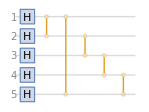

```mathematica
qc = QuantumCircuitOperator["Graph"[CycleGraph[5]]];
qc["Diagram"]
```

Its tableau: the generators are (K̂)_v=(Ẑ)_(v-1)(X̂)_v(Ẑ)_(v+1) around the ring, so the Z block is the adjacency matrix of the cycle:

```mathematica
PauliStabilizer[qc]["TableauForm"]
```

(0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0)

## QuantumInterferometer

Linear optics with exact photon-counting amplitudes: permanents, hafnians and Wigner D-functions in closed form, with angles and photon numbers that can stay symbolic. Below, D_(m m')^j(α,β,γ) is the Wigner D-function, WignerD[{j, m, m'}, α, β, γ].

### 11. A beam splitter, any photon numbers

A beam splitter with symbolic angles, as one object:

```mathematica
bs = QuantumInterferometer[{"BS"[θ, φ]}]
```

QuantumInterferometer[…]

```mathematica
bs["Diagram"]
```

-Graphics-

The amplitude for n_1,n_2 photons in and t_1,t_2 out, every number symbolic, so one result covers every photon-number case, is a conservation delta times one Wigner D-function, A=δ_(n_1+n_2, t_1+t_2) D_((n_1-n_2)/2, t_1-(n_1+n_2)/2)^((n_1+n_2)/2)(φ,2θ,-φ):

```mathematica
bs["Amplitude", {n1, n2} -> {t1, t2}]
```

n1+n2,t1+t2 WignerD[{(n1+n2)/2,(n1-n2)/2,1/2 (-n1-n2+2 t1)},φ,2 θ,-φ]

The same result in traditional notation:

```mathematica
% // TraditionalForm
```

n1+n2,t1+t2 (n1+n2)/2(n1-n2)/21/2 (-n1-n2+2 t1)φ2 θ-φ

Photon numbers can be expressions; 2n photons in one port, n out of each: A(2n,0→n,n)=D_(n, 0)^n(φ,2θ,-φ):

```mathematica
bs["Amplitude", {2 n, 0} -> {n, n}]
```

WignerD[{n,n,0},φ,2 θ,-φ]

```mathematica
% // TraditionalForm
```

nn0φ2 θ-φ

Laser light stays laser light: a coherent state goes to a coherent state, α,β→αcosθ-e^-iφ βsinθ,βcosθ+e^iφ αsinθ:

```mathematica
bs["Coherent"[{α, β}]]
```

Coherent[{α Cos[θ]-ⅇ^(-ⅈ φ) β Sin[θ],β Cos[θ]+ⅇ^(ⅈ φ) α Sin[θ]}]

Its overlap with any coherent state γ,δ is a closed-form Gaussian in their distance, not a sum over truncated Fock states, P=exp (-(γ-αcos θ+e^-iφ βsin θ)^2-(δ-βcos θ-e^iφ αsin θ)^2):

```mathematica
bs["Probability", "Coherent"[{α, β}] -> "Coherent"[{γ, δ}]]
```

ⅇ^(-Abs[δ-β Cos[θ]-ⅇ^(ⅈ φ) α Sin[θ]]^2-Abs[γ-α Cos[θ]+ⅇ^(-ⅈ φ) β Sin[θ]]^2)

Loss only shrinks the amplitude, α→√η α:

```mathematica
QuantumInterferometer[{"Loss"[η]}]["Coherent"[{α}]]
```

Coherent[{α √η}]

### 12. Hong-Ou-Mandel for any n

A balanced (50:50) beam splitter:

```mathematica
bs2 = QuantumInterferometer[{"BS"[Pi/4, 0]}];
bs2["Diagram"]
```

-Graphics-

n photons enter each port. For every n at once, the amplitude for k out of the first is A(n,n→k,2n-k)=D_(0, k-n)^n(0,π/2,0), which vanishes for every odd k: the Hong-Ou-Mandel effect, generalized to any photon number:

```mathematica
bs2["Amplitude", {n, n} -> {k, 2 n - k}]
```

WignerD[{n,0,k-n},0,π/2,0]

The same result in traditional notation:

```mathematica
% // TraditionalForm
```

n0k-n0π/20

### 13. Photon number carried through a network

Two beam splitters in series on the same pair of modes:

```mathematica
chain = QuantumInterferometer[{"BS"[θ1, φ1], "BS"[θ2, φ2]}]
```

QuantumInterferometer[…]

```mathematica
chain["Diagram"]
```

-Graphics-

With n photons in, for every n, the amplitude is an exact sum over the unseen photon number K between the splitters, A(n,0→t,n-t)=∑_(K=0)^n D_(n/2, K-n/2)^(n/2)(φ_1,2 θ_1,-φ_1) D_(K-n/2, t-n/2)^(n/2)(φ_2,2 θ_2,-φ_2):

```mathematica
chain["Amplitude", {n, 0} -> {t, n - t}]
```

WignerD[{n/2,n/2,1/2 (-n+2 K[1])},φ1,2 θ1,-φ1] WignerD[{n/2,1/2 (-n+2 K[1]),1/2 (-n+2 t)},φ2,2 θ2,-φ2]K[1]0n

Substituting n=2, t=1 and evaluating the sum reproduces the concrete two-photon amplitude exactly; the difference is zero:

```mathematica
FullSimplify[Activate[chain["Amplitude", {n, 0} -> {t, n - t}] /. {n -> 2, t -> 1}] - chain["Amplitude", {2, 0} -> {1, 1}]]
```

0

### 14. Three modes, any photon numbers

Three beam splitters across three modes, every angle symbolic:

```mathematica
bs3 = QuantumInterferometer[{"BS"[a1, b1] -> {1, 2}, "BS"[a2, b2] -> {2, 3}, "BS"[a3, b3] -> {1, 2}}, 3]
```

QuantumInterferometer[…]

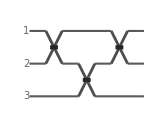

```mathematica
bs3["Diagram"]
```

With N=n_1+n_2 photons in and T=t_1+t_2, the amplitude for arbitrary photon numbers is one conservation delta and a single sum whose upper limit, min (N,T), follows where photons can flow:

A=δ_(N, T+t_3)∑_(K=0)^(min (N,T)) D_((n_1-n_2)/2, K-N/2)^(N/2)(b_1,2 a_1,-b_1) D_((N-K)/2, T-(N+K)/2)^((N-K)/2)(b_2,2 a_2,-b_2) D_(K-T/2, (t_1-t_2)/2)^(T/2)(b_3,2 a_3,-b_3)

```mathematica
bs3["Amplitude", {n1, n2, 0} -> {t1, t2, t3}]
```

n1+n2,t1+t2+t3 WignerD[{(n1+n2)/2,(n1-n2)/2,1/2 (-n1-n2+2 K[1])},b1,2 a1,-b1] WignerD[{(t1+t2)/2,1/2 (-t1-t2+2 K[1]),(t1-t2)/2},b3,2 a3,-b3] WignerD[{1/2 (n1+n2-K[1]),1/2 (n1+n2-K[1]),1/2 (-n1-n2+2 t1+2 t2-K[1])},b2,2 a2,-b2]K[1]0Min[n1+n2,t1+t2]

### 15. Outputs forbidden by symmetry

A four-mode Fourier network, decomposed exactly into beam splitters:

```mathematica
bsFT = QuantumInterferometer[FourierMatrix[4]]
```

QuantumInterferometer[…]

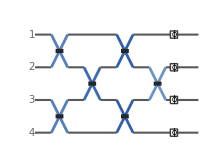

```mathematica
bsFT["Diagram"]
```

One photon in each mode; every output probability, as an exact rational:

```mathematica
p = bsFT["Probabilities", {1, 1, 1, 1}]
```

<|4000→3/32,3100→0,3010→0,3001→0,2200→0,2110→0,2101→1/8,2020→1/16,2011→0,2002→0,1300→0,1210→1/8,1201→0,1120→0,1111→0,1102→0,1030→0,1021→0,1012→1/8,1003→0,0400→3/32,0310→0,0301→0,0220→0,0211→0,0202→1/16,0130→0,0121→1/8,0112→0,0103→0,0040→3/32,0031→0,0022→0,0013→0,0004→3/32|>

The number of output patterns:

```mathematica
Length[p]
```

35

Most never occur, and they come out as exact zeros, not small numbers that floating point would blur into noise. With output modes labelled 0,…,3 and t_j photons in mode j, a pattern is forbidden unless ∑_j j t_j≡0(mod 4), the suppression law of Fourier multiports:

```mathematica
Count[Values[p], 0]
```

25

### 16. Squeezed light

The chance a squeezer emits one photon pair, exact for complex squeezing ξ, P(0→2)=1/2 sech ξ tanh^2 ξ:

```mathematica
QuantumInterferometer[{"S"[ξ]}]["Probability", {0} -> {2}]
```

1/2 Sech[Abs[ξ]] Tanh[Abs[ξ]]^2

Two squeezers meeting at a balanced beam splitter, the building block of Gaussian boson sampling:

```mathematica
bs4 = QuantumInterferometer[{"S"[x1] -> 1, "S"[x2] -> 2, "BS"[Pi/4, 0]}]
```

QuantumInterferometer[…]

```mathematica
bs4["Diagram"]
```

-Graphics-

The coincidence amplitude, A(0,0→1,1)=1/2 √(sech x_1sech x_2) (e^(iarg x_2)tanh x_2-e^(iarg x_1)tanh x_1), vanishes for equal squeezing:

```mathematica
bs4["Amplitude", {0, 0} -> {1, 1}]
```

√(Sech[Abs[x1]] Sech[Abs[x2]]) (-1/2 ⅇ^(ⅈ Arg[x1]) Tanh[Abs[x1]]+1/2 ⅇ^(ⅈ Arg[x2]) Tanh[Abs[x2]])

### 17. A lossy Mach-Zehnder, exactly

Two beam splitters with loss η on the first mode between them, every parameter symbolic:

```mathematica
l2 = QuantumInterferometer[{"BS"[θ, φ], "Loss"[η] -> 1, "BS"[θ2, φ2]}]
```

QuantumInterferometer[…]

```mathematica
l2["Diagram"]
```

-Graphics-

One photon in. Loss enters the exact probabilities: the photon is lost with probability (1-η)cos^2 θ, and the fringe term scales with √η:

P(1,0)=η cos^2 θ cos^2 θ_2+sin^2 θ sin^2 θ_2-2 √η cos θsin θcos θ_2 sin θ_2 cos (φ-φ_2)

```mathematica
l2["Probabilities", {1, 0}]
```

<|00→Cos[θ]^2-η Cos[θ]^2,10→η Cos[θ]^2 Cos[θ2]^2-ⅇ^(-ⅈ (φ-φ2)) √η Cos[θ] Cos[θ2] Sin[θ] Sin[θ2]-ⅇ^(ⅈ φ-ⅈ φ2) √η Cos[θ] Cos[θ2] Sin[θ] Sin[θ2]+Sin[θ]^2 Sin[θ2]^2,01→Cos[θ2]^2 Sin[θ]^2+ⅇ^(-ⅈ (φ-φ2)) √η Cos[θ] Cos[θ2] Sin[θ] Sin[θ2]+ⅇ^(ⅈ φ-ⅈ φ2) √η Cos[θ] Cos[θ2] Sin[θ] Sin[θ2]+η Cos[θ]^2 Sin[θ2]^2|>

Probability is conserved exactly for any angles and loss, proved symbolically rather than checked at sample points:

```mathematica
FullSimplify[Total[l2["Probabilities", {1, 0}]], Element[{θ, φ, θ2, φ2}, Reals] && 0 <= η <= 1]
```

1

### 18. Loss and sampling

Of n photons sent through a lossy channel, k survive with the binomial law P(n→k)=Binomial[n, k] η^k(1-η)^(n-k), derived with n, k and η all symbolic:

```mathematica
QuantumInterferometer[{"Loss"[η]}]["Probability", {n} -> {k}]
```

(1-η)^(-k+n) η^k Binomial[n,k]

Boson sampling, where each exact probability is a permanent and the full table grows explosively: a random 12×12 unitary,

```mathematica
SeedRandom[7];
mat = RandomVariate[CircularUnitaryMatrixDistribution[12]] // UnitaryMatrix
```

UnitaryMatrix[…]

realized as a beam-splitter mesh:

```mathematica
sample = QuantumInterferometer[mat]
```

QuantumInterferometer[…]

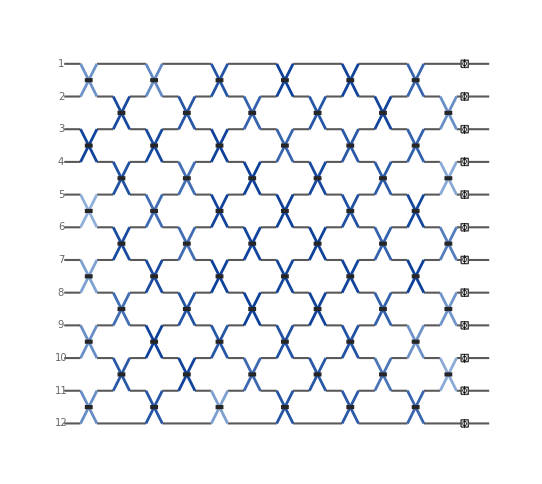

```mathematica
sample["Diagram"]
```

Six photons in, 1000 detector patterns drawn directly with the Clifford-Clifford algorithm, never building the probability table; the twenty most frequent, with their observed frequencies:

```mathematica
ReverseSort[Normalize[Counts@sample["Samples", {1, 1, 1, 1, 1, 1, 0, 0, 0, 0, 0, 0}, 1000], Total]][[;; 20]]
```

<|030000200010→1/250,031200000000→1/250,011002000200→3/1000,100000300101→3/1000,000111012000→3/1000,000201000021→3/1000,000000103011→3/1000,001100201001→3/1000,010210001001→1/500,100100100111→1/500,032100000000→1/500,100000200111→1/500,001000104000→1/500,000000311100→1/500,102010010010→1/500,000010001211→1/500,001021110000→1/500,001100002011→1/500,010010000400→1/500,110000000301→1/500|>